# Dimensional Analysis

Peter Cullen Burbery

Abstract

## Section

XXXX:

## Unit and Quantity Input

### Quantity

```mathematica
Quantity[8,"Meters"]
```

8 m

```mathematica
Quantity[4, "Meters"]
```

4 m

```mathematica
Quantity[12, "Kilograms"]
```

```mathematica
Quantity[40, ("Pascals")/("Newtons")]
```

```mathematica
Quantity[1,"Kilograms"]
```

1 kg

```mathematica
Quantity[1.23,("Kilograms""Meters")/"Seconds"]
```

1.23 kg m/s

```mathematica
Quantity[1,"SpeedOfLight"]
```

c

```mathematica
Quantity[, "GravitationalConstant"]
```

```mathematica
3 Quantity[, "MagneticConstant"]
```

3 μ_0

### QuantityArray

```mathematica
QAMETERS=QuantityArray[{2,3,4},"Meters"]
```

QuantityArray[…]

Extract its magnitudes and units separately:

```mathematica
QuantityMagnitude[QAMETERS]
```

{2,3,4}

```mathematica
QuantityUnit[QAMETERS]
```

{Meters,Meters,Meters}

Normalize the quantity array:

```mathematica
Normal[QAMETERS]
```

{2 m,3 m,4 m}

### Quantity Distribution

Define a distribution for a random height:

```mathematica
𝒟=NormalDistribution[,]
```

QuantityDistribution[NormalDistribution[1200,161], mm]

Compute the probability of a certain height range:

```mathematica
Probability[x>Quantity[1540, "Millimeters"],x\[Distributed]𝒟]
```

1/2 (1-Erf[(170 √2)/161])

```mathematica
NProbability[x>Quantity[1540, "Millimeters"],x\[Distributed]𝒟]
```

0.0173518

Define a distribution of life expectancy:

```mathematica
𝒟=GompertzMakehamDistribution[1/,2.56*10^-4,394.,0];
```

Compute conditional life expectancy:

```mathematica
NExpectation[t\[Conditioned]t>Quantity[8, "Decades"],t\[Distributed]𝒟]
```

86.0983 yr

```mathematica
Table[NExpectation[t\[Conditioned]t>n Quantity[1, "Decades"],t\[Distributed]𝒟],{n,10}]
```

{57.3061 yr,61.9519 yr,66.0996 yr,69.7997 yr,73.215 yr,76.6904 yr,80.7782 yr,86.0983 yr,93.002 yr,101.325 yr}

Fit a model to data with units:

```mathematica
times=Quantity[{2.34,1.55,2.7,0.25,1.5,3.5,3.35,1.85,0.15,2.3,0.65,0.85,5.15},"Minutes"];
```

```mathematica
EstimatedDistribution[times,ExponentialDistribution[λ]]
```

QuantityDistribution[ExponentialDistribution[0.497322], min]

Convert the distribution to another compatible unit:

```mathematica
UnitConvert[,"Hours"]
```

QuantityDistribution[ExponentialDistribution[29.8393], h]

Compare with fitting to distribution in hours:

```mathematica
EstimatedDistribution[times,QuantityDistribution[ExponentialDistribution[λ],"Hours"]]
```

QuantityDistribution[ExponentialDistribution[29.8393], h]

## Applications

The average speed of cars traveling from Champaign Illinois to Chicago Illinois is described by a triangular random variable:

```mathematica
speed𝒟=TriangularDistribution[{,},];
```

Find the expected time of travel:

```mathematica
Expectation[GeoDistance[,]/v,v\[Distributed]speed𝒟]
```

2.48738 h

Define the distribution of a cube's side-length measurements:

```mathematica
ℓ𝒟=BatesDistribution[3,{,}]
```

QuantityDistribution[BatesDistribution[3,{235,243}], mm]

Plot the distribution density:

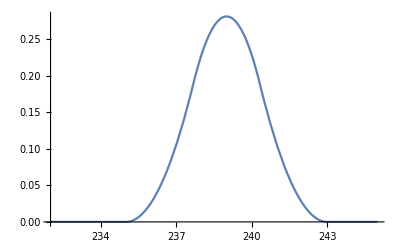

```mathematica
Plot[PDF[ℓ𝒟,Quantity[s,"Millimeters"]]//Evaluate,{s,232,245},Exclusions->None]
```

Compute the mean and the dispersion measures of the cube's volume:

```mathematica
Mean[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]
```

40959581/3 mm^3

```mathematica
Mean[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]//N
```

1.36532×10^7 mm^3

```mathematica
Mean[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]//Round
```

13653194 mm^3

```mathematica
StandardDeviation[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]
```

(4 √(49955519554669/21))/27 mm^3

```mathematica
StandardDeviation[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]//Round
```

228496 mm^3

Plot the PDF of the cube's volume:

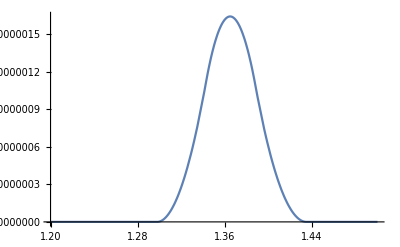

```mathematica
Plot[PDF[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟],Quantity[vol,("Millimeters")^3]]//Evaluate,{vol,1.2*^7 ,1.5*^7},Exclusions->None]
```

Recorded body weights in kilograms:

```mathematica
data=QuantityArray[{67,69,57,78,89,65,57,80,73,66,61,70,64,74,77,69,76,71,75,93,77,78,72,80,63,78,78,52,80,47,70,76,63,77,69,68,48,71,71,69,68,79,67,75,56,62,81,92,63,74,72,90,58,47,58,63,62,73,70,85,61,75,53,59,63,76,78,67,67,83,61,62,75,68,82,65,84,71,49,70,60,72,61,63,84,69,69,52,56,81,78,72,59,67,75,52,67,65,68,60},"Kilograms"];
```

Plot a histogram of the data:

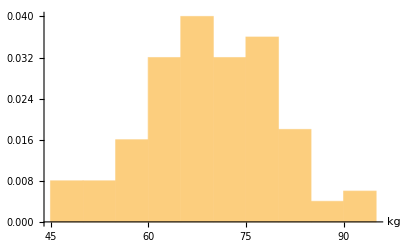

```mathematica
h=Histogram[data,Automatic,"PDF",AxesLabel->Automatic]
```

## Dimensional analysis

```mathematica
SEVENCONSTANTS=<|"Hyper"|>
```

```mathematica
store=EntityStore["Seven defining constants of the SI"-><|
"Entities"-><|
"hyperfine transition frequency of Cs"-><|"Symbol"->"Δν_Cs","Numerical value"->9192631770,"Unit"->"Hz"|>,
"speed of light in vacuum"-><|"Symbol"->"c","Numerical value"->299458792,"Unit"->"m s^-1"|>,"Planck constant"-><|"Symbol"->"h","Numerical value"->6.62607015 10^-34,"Unit"->"J s"|>,"elementary charge"-><|"Symbol"->"e","Numerical value"->1.602176634 10^-19,"Unit"->"C"|>,"Boltzmann constant"-><|"Symbol"->"k","Numerical value"->1.380649 10^-23,"Unit"->"J K^-1"|>,"Avogadro constant"-><|"Symbol"->"N_A","Numerical value"->6.02214076 10^23,"Unit"->"mol^-1"|>,"luminous efficacy"-><|"Symbol"->"K_cd","Numerical value"->683,"Unit"->"lm W^-1"|>
|>
|>]
```

EntityStore[…]

```mathematica
EntityRegister[store]
```

{Seven defining constants of the SI}

```mathematica
InputForm[{"Seven defining constants of the SI"}]
```

{"Seven defining constants of the SI"}

```mathematica
EntityList[First[InputForm[{"Seven defining constants of the SI"}]]]
```

{Seven defining constants of the SI}

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]
```

Boltzmann constant

```mathematica
EntityUnregister[store]
```

```mathematica
EntityUnregister["Seven defining constants of the SI"]
```

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]
```

Entity[Seven defining constants of the SI,Boltzmann constant]

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]["Properties"]
```

{Symbol}

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]["Dataset"]
```

```mathematica
EntityList["Seven defining constants of the SI"]
```

{hyperfine transition frequency of Cs,speed of light in vacuum,Planck constant,elementary charge,Boltzmann constant,Avogadro constant,luminous efficacy}

```mathematica
EntityValue[#,"Dataset"]&/@EntityList["Seven defining constants of the SI"]
```

{,,,,,,}

```mathematica
EntityValue[#,"PropertyAssociation"]&/@EntityList["Seven defining constants of the SI"]
```

{<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>}

```mathematica
(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]
```

{hyperfine transition frequency of Cs→<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,speed of light in vacuum→<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,Planck constant→<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,elementary charge→<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,Boltzmann constant→<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,Avogadro constant→<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,luminous efficacy→<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>}

```mathematica
Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]
```

<|hyperfine transition frequency of Cs→<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,speed of light in vacuum→<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,Planck constant→<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,elementary charge→<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,Boltzmann constant→<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,Avogadro constant→<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,luminous efficacy→<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>|>

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]]
```

```mathematica
BASEUNITS=
```

```mathematica
EntityStore["t"-><|"Entities"->Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]|>]
```

EntityStore[…]

```mathematica
EntityRegister[EntityStore["t"-><|"Entities"->Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]|>]]
```

{t}

```mathematica
EntityList["t"]
```

{hyperfine transition frequency of Cs,speed of light in vacuum,Planck constant,elementary charge,Boltzmann constant,Avogadro constant,luminous efficacy}

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["t"]]]
```

```mathematica
Normal[Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["t"]]]]
```

<|hyperfine transition frequency of Cs→<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,speed of light in vacuum→<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,Planck constant→<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,elementary charge→<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,Boltzmann constant→<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,Avogadro constant→<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,luminous efficacy→<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>|>

```mathematica
EntityUnregister["t"]
```

```mathematica
Normal[Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["t"]]]]
```

Association[(#1→EntityValue[#1,PropertyAssociation]&)/@EntityList[t]]

```mathematica
SIBASEUNITS=EntityStore[<|"SI Base Units"-><|"second"-><|"Base Quantity Name"->"time","Base Quantity Typical Symbol"->"t","Base Unit Name"->"second","Base Unit Symbol"->"s"|>,"meter"-><|"Base Quantity Name"->"length","Base Quantity Typical Symbol"->"l,x,r,etc.","Base Unit Name"->"meter","Base Unit Symbol"->"m" |>,"kilogram"-><|"Base Quantity Name"->"mass","Base Quantity Typical Symbol"->"m","Base Unit Name"->"kilogram","Base Unit Symbol"->"kg"|>,"ampere"-><|"Base Quantity Name"->"electric current","Base Quantity Typical Symbol"->"I,i","Base Unit Name"->"ampere","Base Unit Symbol"->"A"|>,"kelvin"-><|"Base Quantity Name"->"thermodynamic temperature","Base Quantity Typical Symbol"->"T","Base Unit Name"->"kelvin","Base Unit Symbol"->"K"|>,"mole"-><|"Base Quantity Name"->"amount of substance","Base Quantity Typical Symbol"->"n","Base Unit Name"->"mole","Base Unit Symbol"->"mol"|>,"candela"-><|"Base Quantity Name"->"luminous intensity","Base Quantity Typical Symbol"->"I_ν","Base Unit Name"->"candela","Base Unit Symbol"->"cd"|>|>|>]
```

Keys::invrl: The argument Missing[KeyAbsent,Types] is not a valid Association or a list of rules.

EntityStore